```mathematica
d2[n_,k_]:=Sum[d2[j,k-1] d2[n/j,1],{j,Divisors[n]}];d2[n_,1]:=1;d2[1,1]:=0;d2[n_,0]:=0;d2[1,0]:=1
d[n_,z_]:=Product[Pochhammer[z,a=p[[2]]]/a!,{p,FI[n]}];
FI[n_]:=FactorInteger[n];FI[1]:={}
DD[n_,k_]:=Sum[d[j,k],{j,1,n}]

dw[x_, a_] := Sum[ Gamma[a+1]/(Gamma[a-k+1] Gamma[k+1] )d2[x,k],{k,0,Log[2,x]}]
dwk[x_, a_, k_]:= Gamma[a+1]/(Gamma[a-k+1] Gamma[k+1] )d2[x,k]
```

```mathematica
dw[7,5]
```

5

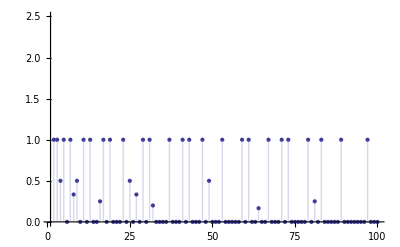

```mathematica
DiscretePlot[ dw[n,.0001]/.0001,{n,1,100}]
```

```mathematica
Gamma[.0001+1]/(Gamma[.0001-2+1] Gamma[2+1] )d2[30,2]
```

-0.00029997

```mathematica
0!
```

1

```mathematica
Expand[(b!)/((k!)(b-k)!)/k]
```

(b!)/(k (b-k)! k!)

```mathematica
FE[b_, k_ ] :=Gamma[b+1]/(Gamma[b-k+1] Gamma[k+1] )/k
```

```mathematica
FE[3,0]
```

Power::infy: Infinite expression 1/0 encountered.

ComplexInfinity

```mathematica
Limit[FE[3,x],x->0]
```

∞

```mathematica
Expand[Gamma[b-k+1]k]
```

k Gamma[1+b-k]

```mathematica
FullSimplify[z(z-1)(z-2)(z-3)/z!]
```

1/Gamma[-3+z]

```mathematica
N[1/Gamma[-3]]
```

0.

```mathematica
Limit[(z-1)/z!,{z->0}]
```

{-1}

```mathematica
Limit[(z-1)(z-2)/z!,{z->0}]
```

{2}

```mathematica
Limit[(z-1)(z-2)(z-3)/z!,{z->0}]
```

{-6}

```mathematica
Limit[(z-1)(z-2)(z-3)(z-4)/z!,{z->0}]
```

{24}

```mathematica
zz[x_] := Log[x]
```

```mathematica
zz'[x]
```

1/x

```mathematica
Series[1/(x+1),{x,0,16}]
```

1-x+x^2-x^3+x^4-x^5+x^6-x^7+x^8-x^9+x^10-x^11+x^12-x^13+x^14-x^15+x^16+O[x]^17

```mathematica
zz[x_] :=1-x+x^2-x^3+x^4-x^5+x^6-x^7+x^8-x^9+x^10-x^11+x^12-x^13+x^14-x^15+x^16
```

```mathematica
Integrate[ zz[n],{n,1,x}]
```

-1768477/2450448+x-x^2/2+x^3/3-x^4/4+x^5/5-x^6/6+x^7/7-x^8/8+x^9/9-x^10/10+x^11/11-x^12/12+x^13/13-x^14/14+x^15/15-x^16/16+x^17/17

```mathematica
Mert[n_] :=Sum[MoebiusMu[j],{j,1,n}]
```

```mathematica
Mert[100]
```

1

```mathematica
MSum[n_] := Sum[ Mert[Floor[n/j]],{j,1,n}]
```

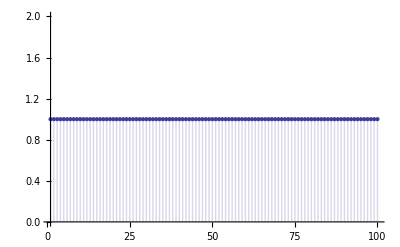

```mathematica
DiscretePlot[ MSum[n],{n,1,100}]
```

```mathematica
cc = -.00000000001
bb[n_] := Sum[ d[ j,-1+cc ]/cc, {j, Divisors[n]}]
```

-1.×10^-11

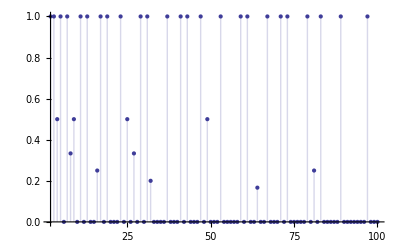

```mathematica
DiscretePlot[ bb[n],{n,2,100}]
```

```mathematica
d[100,-1]
```

0

```mathematica
1+1+1+1+4+.5+4+1+1+2+1.25+4+2+1+1.5+1+3+1+1.5+1.5+2
```

36.25

```mathematica
aaa = -.000000000001
bbb = 100000000000
mm[n_] := (Sum[Mertens[n/j]  d[ j,1+1/bbb ], {j,1,n}]-1)*bbb
mm2[n_] := (Sum[DD[n/j,-1+1/bbb], {j,1,n}]-1)*bbb
Mertens[n_] := Sum[ MoebiusMu[j],{j,1,n}]
```

-1.×10^-12

100000000000

```mathematica
N[mm[100]]
```

28.5333

28.5333

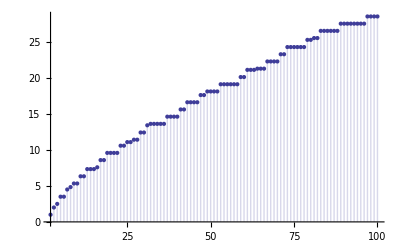

```mathematica
N[mm2[100]]

DiscretePlot[ mm2[n],{n,2,100}]
```

```mathematica
d[10,1+10^-20]/10^-20
```

10000000000000000000200000000000000000001/100000000000000000000

```mathematica
Limit[ 1/x^z-1
```

```mathematica
FF[x_] :=  x^0/0! P0+x^1/1! P1+x^2/2! P2+x^3/3! P3+x^4/4! P4+x^5/5! P5+x^6/6! P6+x^7/7! P7+x^8/8! P8+x^9/9! P9
```

```mathematica
Derivative[2][FF]/. #1 -> x
```

P2+P3 x+(P4 x^2)/2+(P5 x^3)/6+(P6 x^4)/24+(P7 x^5)/120+(P8 x^6)/720+(P9 x^7)/5040&

```mathematica
Dwh[x_, a_] := Sum[ Gamma[a+1]/(Gamma[a-k+1] Gamma[k+1] ) Dhyp[x,k],{k,0,Log[2,x]}]
```

```mathematica
Dwh2[a_] := Dwh[x,a]
```

```mathematica
Derivative[-1][Dwh2] /. #1->a
```

Dwh2^(-1)

```mathematica
FE[n_] :=Sum[ d[j,aaa] Log[j],{j,2,n}]/aaa
```

```mathematica
FE[100]
```

```mathematica
94.0456347612684
```

```mathematica
ML[j_, x_ ] := ((j^x-1)/x)(d[j,x]/x)
```

```mathematica
{ML[zz=6,.00000001],N[MangoldtLambda[zz]]}
```

{1.79176×10^-8,0.}

```mathematica
N[Log[3]]
```

1.09861

```mathematica
FullSimplify[((j^x-1)/x)(d[j,x]/x)]
```

FactorInteger::exact: Argument j in FactorInteger[j] is not an exact number.

Part::partd: Part specification p ⟦ 2 ⟧ is longer than depth of object.

FactorInteger::exact: Argument j in FactorInteger[j] is not an exact number.

Part::partd: Part specification p ⟦ 2 ⟧ is longer than depth of object.

((-1+j^x) ∏_p^FactorInteger[j] Pochhammer[x,p⟦2⟧]/(p⟦2⟧!))/x^2